```mathematica
parse[s_]:=ToExpression@StringReplace[s,{"("->"{",")"->"}","Vector("->"{","E"->"*10^"}]
```

```mathematica
model=a x^n+c;
```

```mathematica
(*model=a n^x+c;*)
```

```mathematica
fitDegree[data_]:=FindFit[data,model,{a,n,c},x]
```

```mathematica
plotTogehter[data_, rule_]:=With[{expr=model/.rule},
Show[
Plot[expr,{x,data[[1,1]],data[[-1,1]]}],
ListPlot[data,PlotStyle->Red],PlotLabel->expr]]
```

```mathematica
fitAndPlot[data_]:=plotTogehter[data,fitDegree[data]]
```

```mathematica
s="Vector((55.0,1239.0), (143.0,15922.0), (187.0,30640.0), (215.0,42526.0), (295.0,87286.0), (335.0,115666.0), (351.0,128138.0), (419.0,188284.0), (451.0,220588.0), (519.0,297734.0))";
```

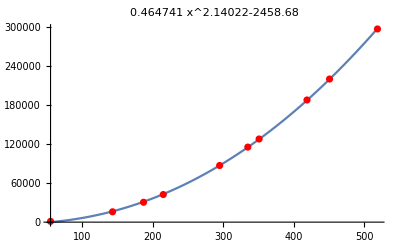

```mathematica
fitAndPlot[parse[s]]
```